```mathematica
Es = {0, -g μ H+Δ,Δ,g μ H+Δ, -2 g μ H+3 Δ,-g μ H+3 Δ, 3 Δ, g μ H+3 Δ, 2 g μ H+3 Δ, -3 g μ H+6 Δ,-2 g μ H+6 Δ,-g μ H+6 Δ, 6 Δ, g μ H+6 Δ, 2 g μ H+6 Δ, 3 g μ H+6 Δ};
Ms=-D[Es, H]
```

```mathematica
{0,g μ,0,-g μ,2 g μ,g μ,0,-g μ,-2 g μ,3 g μ,2 g μ,g μ,0,-g μ,-2 g μ,-3 g μ}
```

```mathematica
arr=Es/.{g->2, μ->0.97, H->1, Δ->5}
```

{0,3.06,5,6.94,11.12,13.06,15,16.94,18.88,24.18,26.12,28.06,30,31.94,33.88,35.82}

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

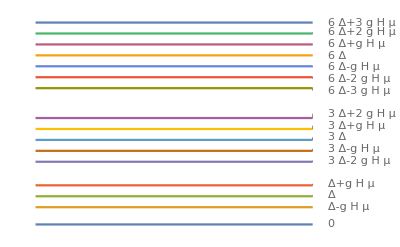

```mathematica
Plot[{0,3.06,5,6.9399999999999995,11.120000000000001,13.06,15,16.94,18.88,24.18,26.12,28.06,30,31.94,33.88,35.82} ,{x,0,1}, Axes->False, PlotLabels->{0, -g μ H+Δ,Δ,g μ H+Δ, -2 g μ H+3 Δ,-g μ H+3 Δ, 3 Δ, g μ H+3 Δ, 2 g μ H+3 Δ, -3 g μ H+6 Δ,-2 g μ H+6 Δ,-g μ H+6 Δ, 6 Δ, g μ H+6 Δ, 2 g μ H+6 Δ, 3 g μ H+6 Δ}]
```

```mathematica
arr2={0, -g μ H+Δ,Δ,g μ H+Δ}/.{g->2, μ->0.97, H->1, Δ->5};
```

```mathematica
{"0", "-g μ H+Δ","Δ","g μ H+Δ"}
```

```mathematica
arr2
```

{0,3.06,5,6.94}

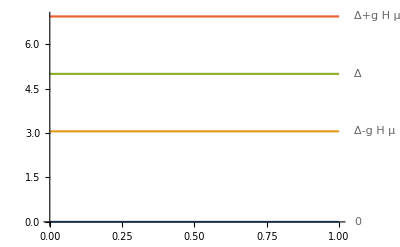

```mathematica
Plot[ {0,3.06,5,6.9399999999999995},{x,0,1}, PlotLabels->{0, -g μ H+Δ,Δ,g μ H+Δ}]
```

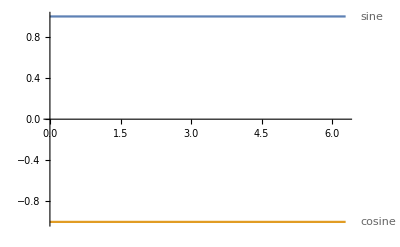

```mathematica
Plot[{1,-1},{x,0,2π},PlotLabels->{"sine","cosine"}]
```

```mathematica
DiscretePlot
```

```mathematica
chisl = 0;
z =0;
For[i=1, i≤ Length[Es], ++i, 
chisl+=Ms[[i]]*ⅇ^((-Es[[i]])/(k T));
z +=ⅇ^((-Es[[i]])/(k T));

];
```

```mathematica
u=chisl/z //Simplify
```

((-1+ⅇ^((2 g H μ)/(k T))) (3+2 ⅇ^((g H μ)/(k T))+4 ⅇ^((2 g H μ)/(k T))+2 ⅇ^((3 g H μ)/(k T))+3 ⅇ^((4 g H μ)/(k T))+2 ⅇ^((3 (Δ+g H μ))/(k T))+2 ⅇ^((3 Δ+g H μ)/(k T))+ⅇ^((3 Δ+2 g H μ)/(k T))+ⅇ^((5 Δ+2 g H μ)/(k T))) g μ)/(1+ⅇ^((g H μ)/(k T))+ⅇ^((2 g H μ)/(k T))+ⅇ^((3 g H μ)/(k T))+ⅇ^((4 g H μ)/(k T))+ⅇ^((5 g H μ)/(k T))+ⅇ^((6 g H μ)/(k T))+ⅇ^((3 (Δ+g H μ))/(k T))+ⅇ^((3 Δ+g H μ)/(k T))+ⅇ^((3 Δ+2 g H μ)/(k T))+ⅇ^((5 Δ+2 g H μ)/(k T))+ⅇ^((5 Δ+3 g H μ)/(k T))+ⅇ^((6 Δ+3 g H μ)/(k T))+ⅇ^((3 Δ+4 g H μ)/(k T))+ⅇ^((5 Δ+4 g H μ)/(k T))+ⅇ^((3 Δ+5 g H μ)/(k T)))

```mathematica
x1 =μ/k;
```

```mathematica
chisl = (-1+ⅇ^((2 g H x1)/T)) (3+2 ⅇ^((g H x1)/T)+4 ⅇ^((2 g H x1)/T)+2 ⅇ^((3 g H x1)/T)+3 ⅇ^((4 g H x1)/T)+2 ⅇ^((3 (Δ+g H x1))/T)+2 ⅇ^((3 Δ+g H x1)/T)+ⅇ^((3 Δ+2 g H x1)/T)+ⅇ^((5 Δ+2 g H x1)/T)) g μ;
znam = 1+ⅇ^((g H x1)/T)+ⅇ^((2 g H x1)/T)+ⅇ^((3 g H x1)/T)+ⅇ^((4 g H x1)/T)+ⅇ^((5 g H x1)/T)+ⅇ^((6 g H x1)/T)+ⅇ^((3 (Δ+g H x1))/T)+ⅇ^((3 Δ+g H x1)/T)+ⅇ^((3 Δ+2 g H x1)/T)+ⅇ^((5 Δ+2 g H x1)/T)+ⅇ^((5 Δ+3 g H x1)/T)+ⅇ^((6 Δ+3 g H x1)/T)+ⅇ^((3 Δ+4 g H x1)/T)+ⅇ^((5 Δ+4 g H x1)/T)+ⅇ^((3 Δ+5 g H x1)/T);
u1 = chisl/znam
```

((-1+ⅇ^((2 g H μ)/(k T))) (3+2 ⅇ^((g H μ)/(k T))+4 ⅇ^((2 g H μ)/(k T))+2 ⅇ^((3 g H μ)/(k T))+3 ⅇ^((4 g H μ)/(k T))+2 ⅇ^((3 (Δ+(g H μ)/k))/T)+2 ⅇ^((3 Δ+(g H μ)/k)/T)+ⅇ^((3 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(2 g H μ)/k)/T)) g μ)/(1+ⅇ^((g H μ)/(k T))+ⅇ^((2 g H μ)/(k T))+ⅇ^((3 g H μ)/(k T))+ⅇ^((4 g H μ)/(k T))+ⅇ^((5 g H μ)/(k T))+ⅇ^((6 g H μ)/(k T))+ⅇ^((3 (Δ+(g H μ)/k))/T)+ⅇ^((3 Δ+(g H μ)/k)/T)+ⅇ^((3 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(3 g H μ)/k)/T)+ⅇ^((6 Δ+(3 g H μ)/k)/T)+ⅇ^((3 Δ+(4 g H μ)/k)/T)+ⅇ^((5 Δ+(4 g H μ)/k)/T)+ⅇ^((3 Δ+(5 g H μ)/k)/T))

```mathematica
χ=Limit[D[u,H],H->0]
```

(2 (14+5 ⅇ^((3 Δ)/(k T))+ⅇ^((5 Δ)/(k T))) g^2 μ^2)/((7+5 ⅇ^((3 Δ)/(k T))+3 ⅇ^((5 Δ)/(k T))+ⅇ^((6 Δ)/(k T))) k T)

```mathematica
C1=(R*D[T^2*D[Log[znam],T],T] )
```

R ((2 T (-(ⅇ^((g H μ)/(k T)) g H μ)/(k T^2)-(2 ⅇ^((2 g H μ)/(k T)) g H μ)/(k T^2)-(3 ⅇ^((3 g H μ)/(k T)) g H μ)/(k T^2)-(4 ⅇ^((4 g H μ)/(k T)) g H μ)/(k T^2)-(5 ⅇ^((5 g H μ)/(k T)) g H μ)/(k T^2)-(6 ⅇ^((6 g H μ)/(k T)) g H μ)/(k T^2)-(3 ⅇ^((3 (Δ+(g H μ)/k))/T) (Δ+(g H μ)/k))/T^2-(ⅇ^((3 Δ+(g H μ)/k)/T) (3 Δ+(g H μ)/k))/T^2-(ⅇ^((3 Δ+(2 g H μ)/k)/T) (3 Δ+(2 g H μ)/k))/T^2-(ⅇ^((5 Δ+(2 g H μ)/k)/T) (5 Δ+(2 g H μ)/k))/T^2-(ⅇ^((5 Δ+(3 g H μ)/k)/T) (5 Δ+(3 g H μ)/k))/T^2-(ⅇ^((6 Δ+(3 g H μ)/k)/T) (6 Δ+(3 g H μ)/k))/T^2-(ⅇ^((3 Δ+(4 g H μ)/k)/T) (3 Δ+(4 g H μ)/k))/T^2-(ⅇ^((5 Δ+(4 g H μ)/k)/T) (5 Δ+(4 g H μ)/k))/T^2-(ⅇ^((3 Δ+(5 g H μ)/k)/T) (3 Δ+(5 g H μ)/k))/T^2))/(1+ⅇ^((g H μ)/(k T))+ⅇ^((2 g H μ)/(k T))+ⅇ^((3 g H μ)/(k T))+ⅇ^((4 g H μ)/(k T))+ⅇ^((5 g H μ)/(k T))+ⅇ^((6 g H μ)/(k T))+ⅇ^((3 (Δ+(g H μ)/k))/T)+ⅇ^((3 Δ+(g H μ)/k)/T)+ⅇ^((3 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(3 g H μ)/k)/T)+ⅇ^((6 Δ+(3 g H μ)/k)/T)+ⅇ^((3 Δ+(4 g H μ)/k)/T)+ⅇ^((5 Δ+(4 g H μ)/k)/T)+ⅇ^((3 Δ+(5 g H μ)/k)/T))-(T^2 (-(ⅇ^((g H μ)/(k T)) g H μ)/(k T^2)-(2 ⅇ^((2 g H μ)/(k T)) g H μ)/(k T^2)-(3 ⅇ^((3 g H μ)/(k T)) g H μ)/(k T^2)-(4 ⅇ^((4 g H μ)/(k T)) g H μ)/(k T^2)-(5 ⅇ^((5 g H μ)/(k T)) g H μ)/(k T^2)-(6 ⅇ^((6 g H μ)/(k T)) g H μ)/(k T^2)-(3 ⅇ^((3 (Δ+(g H μ)/k))/T) (Δ+(g H μ)/k))/T^2-(ⅇ^((3 Δ+(g H μ)/k)/T) (3 Δ+(g H μ)/k))/T^2-(ⅇ^((3 Δ+(2 g H μ)/k)/T) (3 Δ+(2 g H μ)/k))/T^2-(ⅇ^((5 Δ+(2 g H μ)/k)/T) (5 Δ+(2 g H μ)/k))/T^2-(ⅇ^((5 Δ+(3 g H μ)/k)/T) (5 Δ+(3 g H μ)/k))/T^2-(ⅇ^((6 Δ+(3 g H μ)/k)/T) (6 Δ+(3 g H μ)/k))/T^2-(ⅇ^((3 Δ+(4 g H μ)/k)/T) (3 Δ+(4 g H μ)/k))/T^2-(ⅇ^((5 Δ+(4 g H μ)/k)/T) (5 Δ+(4 g H μ)/k))/T^2-(ⅇ^((3 Δ+(5 g H μ)/k)/T) (3 Δ+(5 g H μ)/k))/T^2)^2)/(1+ⅇ^((g H μ)/(k T))+ⅇ^((2 g H μ)/(k T))+ⅇ^((3 g H μ)/(k T))+ⅇ^((4 g H μ)/(k T))+ⅇ^((5 g H μ)/(k T))+ⅇ^((6 g H μ)/(k T))+ⅇ^((3 (Δ+(g H μ)/k))/T)+ⅇ^((3 Δ+(g H μ)/k)/T)+ⅇ^((3 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(3 g H μ)/k)/T)+ⅇ^((6 Δ+(3 g H μ)/k)/T)+ⅇ^((3 Δ+(4 g H μ)/k)/T)+ⅇ^((5 Δ+(4 g H μ)/k)/T)+ⅇ^((3 Δ+(5 g H μ)/k)/T))^2+(T^2 ((2 ⅇ^((g H μ)/(k T)) g H μ)/(k T^3)+(4 ⅇ^((2 g H μ)/(k T)) g H μ)/(k T^3)+(6 ⅇ^((3 g H μ)/(k T)) g H μ)/(k T^3)+(8 ⅇ^((4 g H μ)/(k T)) g H μ)/(k T^3)+(10 ⅇ^((5 g H μ)/(k T)) g H μ)/(k T^3)+(12 ⅇ^((6 g H μ)/(k T)) g H μ)/(k T^3)+(ⅇ^((g H μ)/(k T)) g^2 H^2 μ^2)/(k^2 T^4)+(4 ⅇ^((2 g H μ)/(k T)) g^2 H^2 μ^2)/(k^2 T^4)+(9 ⅇ^((3 g H μ)/(k T)) g^2 H^2 μ^2)/(k^2 T^4)+(16 ⅇ^((4 g H μ)/(k T)) g^2 H^2 μ^2)/(k^2 T^4)+(25 ⅇ^((5 g H μ)/(k T)) g^2 H^2 μ^2)/(k^2 T^4)+(36 ⅇ^((6 g H μ)/(k T)) g^2 H^2 μ^2)/(k^2 T^4)+(6 ⅇ^((3 (Δ+(g H μ)/k))/T) (Δ+(g H μ)/k))/T^3+(9 ⅇ^((3 (Δ+(g H μ)/k))/T) (Δ+(g H μ)/k)^2)/T^4+(2 ⅇ^((3 Δ+(g H μ)/k)/T) (3 Δ+(g H μ)/k))/T^3+(ⅇ^((3 Δ+(g H μ)/k)/T) (3 Δ+(g H μ)/k)^2)/T^4+(2 ⅇ^((3 Δ+(2 g H μ)/k)/T) (3 Δ+(2 g H μ)/k))/T^3+(ⅇ^((3 Δ+(2 g H μ)/k)/T) (3 Δ+(2 g H μ)/k)^2)/T^4+(2 ⅇ^((5 Δ+(2 g H μ)/k)/T) (5 Δ+(2 g H μ)/k))/T^3+(ⅇ^((5 Δ+(2 g H μ)/k)/T) (5 Δ+(2 g H μ)/k)^2)/T^4+(2 ⅇ^((5 Δ+(3 g H μ)/k)/T) (5 Δ+(3 g H μ)/k))/T^3+(ⅇ^((5 Δ+(3 g H μ)/k)/T) (5 Δ+(3 g H μ)/k)^2)/T^4+(2 ⅇ^((6 Δ+(3 g H μ)/k)/T) (6 Δ+(3 g H μ)/k))/T^3+(ⅇ^((6 Δ+(3 g H μ)/k)/T) (6 Δ+(3 g H μ)/k)^2)/T^4+(2 ⅇ^((3 Δ+(4 g H μ)/k)/T) (3 Δ+(4 g H μ)/k))/T^3+(ⅇ^((3 Δ+(4 g H μ)/k)/T) (3 Δ+(4 g H μ)/k)^2)/T^4+(2 ⅇ^((5 Δ+(4 g H μ)/k)/T) (5 Δ+(4 g H μ)/k))/T^3+(ⅇ^((5 Δ+(4 g H μ)/k)/T) (5 Δ+(4 g H μ)/k)^2)/T^4+(2 ⅇ^((3 Δ+(5 g H μ)/k)/T) (3 Δ+(5 g H μ)/k))/T^3+(ⅇ^((3 Δ+(5 g H μ)/k)/T) (3 Δ+(5 g H μ)/k)^2)/T^4))/(1+ⅇ^((g H μ)/(k T))+ⅇ^((2 g H μ)/(k T))+ⅇ^((3 g H μ)/(k T))+ⅇ^((4 g H μ)/(k T))+ⅇ^((5 g H μ)/(k T))+ⅇ^((6 g H μ)/(k T))+ⅇ^((3 (Δ+(g H μ)/k))/T)+ⅇ^((3 Δ+(g H μ)/k)/T)+ⅇ^((3 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(2 g H μ)/k)/T)+ⅇ^((5 Δ+(3 g H μ)/k)/T)+ⅇ^((6 Δ+(3 g H μ)/k)/T)+ⅇ^((3 Δ+(4 g H μ)/k)/T)+ⅇ^((5 Δ+(4 g H μ)/k)/T)+ⅇ^((3 Δ+(5 g H μ)/k)/T)))

```mathematica
(R (-2  s1 T s2-s3+s1 s4))/(s1^2 T^2)
```

```mathematica
C1=(R*(-2*s1*T*s2-s3+s1*s4))/(s1^2* T^2 )
```

```mathematica
s1 =1+ⅇ^((g H x1)/T)+ⅇ^((2 g H x1)/T)+ⅇ^((3 g H x1)/T)+ⅇ^((4 g H x1)/T)+ⅇ^((5 g H x1)/T)+ⅇ^((6 g H x1)/T)+ⅇ^((3 (g H x1+Δ))/T)+ⅇ^((g H x1+3 Δ)/T)+ⅇ^((2 g H x1+3 Δ)/T)+ⅇ^((4 g H x1+3 Δ)/T)+ⅇ^((5 g H x1+3 Δ)/T)+ⅇ^((2 g H x1+5 Δ)/T)+ⅇ^((3 g H x1+5 Δ)/T)+ⅇ^((4 g H x1+5 Δ)/T)+ⅇ^((3 g H x1+6 Δ)/T)
```

1+ⅇ^((g H x1)/T)+ⅇ^((2 g H x1)/T)+ⅇ^((3 g H x1)/T)+ⅇ^((4 g H x1)/T)+ⅇ^((5 g H x1)/T)+ⅇ^((6 g H x1)/T)+ⅇ^((3 (g H x1+Δ))/T)+ⅇ^((g H x1+3 Δ)/T)+ⅇ^((2 g H x1+3 Δ)/T)+ⅇ^((4 g H x1+3 Δ)/T)+ⅇ^((5 g H x1+3 Δ)/T)+ⅇ^((2 g H x1+5 Δ)/T)+ⅇ^((3 g H x1+5 Δ)/T)+ⅇ^((4 g H x1+5 Δ)/T)+ⅇ^((3 g H x1+6 Δ)/T)

```mathematica
s2 =ⅇ^((g H x1)/T) g H x1+2 ⅇ^((2 g H x1)/T) g H x1+3 ⅇ^((3 g H x1)/T) g H x1+4 ⅇ^((4 g H x1)/T) g H x1+5 ⅇ^((5 g H x1)/T) g H x1+6 ⅇ^((6 g H x1)/T) g H x1+3 ⅇ^((3 (g H x1+Δ))/T) (g H x1+Δ)+3 ⅇ^((3 g H x1+6 Δ)/T) (g H x1+2 Δ)+ⅇ^((g H x1+3 Δ)/T) (g H x1+3 Δ)+ⅇ^((2 g H x1+3 Δ)/T) (2 g H x1+3 Δ)+ⅇ^((4 g H x1+3 Δ)/T) (4 g H x1+3 Δ)+ⅇ^((5 g H x1+3 Δ)/T) (5 g H x1+3 Δ)+ⅇ^((2 g H x1+5 Δ)/T) (2 g H x1+5 Δ)+ⅇ^((3 g H x1+5 Δ)/T) (3 g H x1+5 Δ)+ⅇ^((4 g H x1+5 Δ)/T) (4 g H x1+5 Δ)
```

ⅇ^((g H x1)/T) g H x1+2 ⅇ^((2 g H x1)/T) g H x1+3 ⅇ^((3 g H x1)/T) g H x1+4 ⅇ^((4 g H x1)/T) g H x1+5 ⅇ^((5 g H x1)/T) g H x1+6 ⅇ^((6 g H x1)/T) g H x1+3 ⅇ^((3 (g H x1+Δ))/T) (g H x1+Δ)+3 ⅇ^((3 g H x1+6 Δ)/T) (g H x1+2 Δ)+ⅇ^((g H x1+3 Δ)/T) (g H x1+3 Δ)+ⅇ^((2 g H x1+3 Δ)/T) (2 g H x1+3 Δ)+ⅇ^((4 g H x1+3 Δ)/T) (4 g H x1+3 Δ)+ⅇ^((5 g H x1+3 Δ)/T) (5 g H x1+3 Δ)+ⅇ^((2 g H x1+5 Δ)/T) (2 g H x1+5 Δ)+ⅇ^((3 g H x1+5 Δ)/T) (3 g H x1+5 Δ)+ⅇ^((4 g H x1+5 Δ)/T) (4 g H x1+5 Δ)

```mathematica
s3=(ⅇ^((g H x1)/T) g H x1+2 ⅇ^((2 g H x1)/T) g H x1+3 ⅇ^((3 g H x1)/T) g H x1+4 ⅇ^((4 g H x1)/T) g H x1+5 ⅇ^((5 g H x1)/T) g H x1+6 ⅇ^((6 g H x1)/T) g H x1+3 ⅇ^((3 (g H x1+Δ))/T) (g H x1+Δ)+3 ⅇ^((3 g H x1+6 Δ)/T) (g H x1+2 Δ)+ⅇ^((g H x1+3 Δ)/T) (g H x1+3 Δ)+ⅇ^((2 g H x1+3 Δ)/T) (2 g H x1+3 Δ)+ⅇ^((4 g H x1+3 Δ)/T) (4 g H x1+3 Δ)+ⅇ^((5 g H x1+3 Δ)/T) (5 g H x1+3 Δ)+ⅇ^((2 g H x1+5 Δ)/T) (2 g H x1+5 Δ)+ⅇ^((3 g H x1+5 Δ)/T) (3 g H x1+5 Δ)+ⅇ^((4 g H x1+5 Δ)/T) (4 g H x1+5 Δ))^2 /.{T->1, Δ->D0}
```

(ⅇ^(g H x1) g H x1+2 ⅇ^(2 g H x1) g H x1+3 ⅇ^(3 g H x1) g H x1+4 ⅇ^(4 g H x1) g H x1+5 ⅇ^(5 g H x1) g H x1+6 ⅇ^(6 g H x1) g H x1+3 ⅇ^(3 (D0+g H x1)) (D0+g H x1)+3 ⅇ^(6 D0+3 g H x1) (2 D0+g H x1)+ⅇ^(3 D0+g H x1) (3 D0+g H x1)+ⅇ^(3 D0+2 g H x1) (3 D0+2 g H x1)+ⅇ^(5 D0+2 g H x1) (5 D0+2 g H x1)+ⅇ^(5 D0+3 g H x1) (5 D0+3 g H x1)+ⅇ^(3 D0+4 g H x1) (3 D0+4 g H x1)+ⅇ^(5 D0+4 g H x1) (5 D0+4 g H x1)+ⅇ^(3 D0+5 g H x1) (3 D0+5 g H x1))^2

```mathematica
s4=4 ⅇ^((2 g H x1)/T) g H x1 (T+g H x1)+ⅇ^((g H x1)/T) g H x1 (2 T+g H x1)+8 ⅇ^((4 g H x1)/T) g H x1 (T+2 g H x1)+12 ⅇ^((6 g H x1)/T) g H x1 (T+3 g H x1)+3 ⅇ^((3 g H x1)/T) g H x1 (2 T+3 g H x1)+5 ⅇ^((5 g H x1)/T) g H x1 (2 T+5 g H x1)+ⅇ^((g H x1+3 Δ)/T) (g H x1+3 Δ) (2 T+g H x1+3 Δ)+ⅇ^((2 g H x1+3 Δ)/T) (2 g H x1+3 Δ) (2 T+2 g H x1+3 Δ)+ⅇ^((4 g H x1+3 Δ)/T) (4 g H x1+3 Δ) (2 T+4 g H x1+3 Δ)+ⅇ^((5 g H x1+3 Δ)/T) (5 g H x1+3 Δ) (2 T+5 g H x1+3 Δ)+ⅇ^((2 g H x1+5 Δ)/T) (2 g H x1+5 Δ) (2 T+2 g H x1+5 Δ)+ⅇ^((3 g H x1+5 Δ)/T) (3 g H x1+5 Δ) (2 T+3 g H x1+5 Δ)+ⅇ^((4 g H x1+5 Δ)/T) (4 g H x1+5 Δ) (2 T+4 g H x1+5 Δ)+3 ⅇ^((3 g H x1+6 Δ)/T) (g H x1+2 Δ) (2 T+3 g H x1+6 Δ)+3 ⅇ^((3 (g H x1+Δ))/T) (g H x1+Δ) (2 T+3 (g H x1+Δ)) /.{T->1,Δ-> D0}
```

4 ⅇ^(2 g H x1) g H x1 (1+g H x1)+ⅇ^(g H x1) g H x1 (2+g H x1)+ⅇ^(3 D0+g H x1) (3 D0+g H x1) (2+3 D0+g H x1)+8 ⅇ^(4 g H x1) g H x1 (1+2 g H x1)+ⅇ^(3 D0+2 g H x1) (3 D0+2 g H x1) (2+3 D0+2 g H x1)+ⅇ^(5 D0+2 g H x1) (5 D0+2 g H x1) (2+5 D0+2 g H x1)+12 ⅇ^(6 g H x1) g H x1 (1+3 g H x1)+3 ⅇ^(3 g H x1) g H x1 (2+3 g H x1)+ⅇ^(5 D0+3 g H x1) (5 D0+3 g H x1) (2+5 D0+3 g H x1)+3 ⅇ^(6 D0+3 g H x1) (2 D0+g H x1) (2+6 D0+3 g H x1)+ⅇ^(3 D0+4 g H x1) (3 D0+4 g H x1) (2+3 D0+4 g H x1)+ⅇ^(5 D0+4 g H x1) (5 D0+4 g H x1) (2+5 D0+4 g H x1)+5 ⅇ^(5 g H x1) g H x1 (2+5 g H x1)+ⅇ^(3 D0+5 g H x1) (3 D0+5 g H x1) (2+3 D0+5 g H x1)+3 ⅇ^(3 (D0+g H x1)) (D0+g H x1) (2+3 (D0+g H x1))

```mathematica
4*exp(2*2*Col(H1)*Col(x1))*2*Col(H1)*Col(x1)*(1+2*Col(H1)*Col(x1))+exp(2*Col(H1)*Col(x1))*2*Col(H1)*Col(x1)*(2+2*Col(H1)*Col(x1))+exp(3*Col(x2)+2*Col(H1)*Col(x1))*(3*Col(D0)+2*Col(H1)*Col(x1))*(2+3*Col(D0)+2*Col(H1)*Col(x1))+8*exp(4*2*Col(H1)*Col(x1))*2*Col(H1)*Col(x1)*(1+2*2*Col(H1)*Col(x1))+exp(3*Col(x2)+2*2*Col(H1)*Col(x1))*(3*Col(D0)+2*2*Col(H1)*Col(x1))*(2+3*Col(D0)+2*2*Col(H1)*Col(x1))+exp(5*Col(x2)+2*2*Col(H1)*Col(x1))*(5*Col(D0)+2*2*Col(H1)*Col(x1))*(2+5*Col(D0)+2*2*Col(H1)*Col(x1))+12*exp(6*2*Col(H1)*Col(x1))*2*Col(H1)*Col(x1)*(1+3*2*Col(H1)*Col(x1))+3*exp(3*2*Col(H1)*Col(x1))*2*Col(H1)*Col(x1)*(2+3*2*Col(H1)*Col(x1))+exp(5*Col(x2)+3*2*Col(H1)*Col(x1))*(5*Col(D0)+3*2*Col(H1)*Col(x1))*(2+5*Col(D0)+3*2*Col(H1)*Col(x1))+3*exp(6*Col(x2)+3*2*Col(H1)*Col(x1))*(2*Col(D0)+2*Col(H1)*Col(x1))*(2+6*Col(D0)+3*2*Col(H1)*Col(x1))+exp(3*Col(x2)+4*2*Col(H1)*Col(x1))*(3*Col(D0)+4*2*Col(H1)*Col(x1))*(2+3*Col(D0)+4*2*Col(H1)*Col(x1))+exp(5*Col(x2)+4*2*Col(H1)*Col(x1))*(5*Col(D0)+4*2*Col(H1)*Col(x1))*(2+5*Col(D0)+4*2*Col(H1)*Col(x1))+5*exp(5*2*Col(H1)*Col(x1))*2*Col(H1)*Col(x1)*(2+5*2*Col(H1)*Col(x1))+exp(3*Col(x2)+5*2*Col(H1)*Col(x1))*(3*Col(D0)+5*2*Col(H1)*Col(x1))*(2+3*Col(D0)+5*2*Col(H1)*Col(x1))+3*exp(3*(Col(x2)+2*Col(H1)*Col(x1)))*(Col(D0)+2*Col(H1)*Col(x1))*(2+3*(Col(D0)+2*Col(H1)*Col(x1)))
```